Asumo que capturo varios períodos (>>10), de una señal periódica (o casi). Le hago la DFT, y sumo un intervalo de 9 puntos alrededor de los máximos locales, que chequeo, tengan frecuencias aproximadamente múltiplas, con cierta tolerancia.
No asumo que las muestras vienen equiespaciadas. Las transformo en uniformes con interpolación de orden 3. Remuestreo con el doble de puntos que la original.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
data=SemanticImport["Clase G par doble +15-15-0.5vin-4ohm.txt"][All, Values]//Normal;
```

```mathematica
ts=TimeSeries[data, ResamplingMethod->{"Interpolation",InterpolationOrder->0}]
```

TimeSeries[…]

```mathematica
resample[ts_]:=ts[ts["FirstTime"] +(ts["LastTime"]-ts["FirstTime"])Range[0, 2 ts["PathLength"]]/(2 ts["PathLength"])];
```

```mathematica
halfLenght[l_List]:=l~Take~Ceiling[Length@l/2];
```

```mathematica
fftpot[ts_TemporalData]:=Abs[Fourier[(*PadRight[*)resample[ts](*, 2^Ceiling[Log2[3 ts["PathLength"]]]]*)]]^2//halfLenght;
```

```mathematica
potHarm[n_,Null,neig_:9][fftpot_]:=potHarm[n, First@Ordering[fftpot, -1]-1, neig];
potHarm[n_, fftstep_, neig_:9][fftpot_]:=Total[Take[fftpot,1+n fftstep+Round[{-1, 1} (neig-1)/2]]]
```

Luego, la distorsión

```mathematica
distortion[ts_TemporalData]:=With[{fpot=fftpot[ts]},
With[{fftstep=First@Ordering[fpot, -1]-1},

Table[potHarm[n,fftstep, 9][fpot], {n, 1, Min[50,Floor[ Length[fpot]/fftstep]]}]/.{fund_,harms___}:>√(Total[{harms}]/fund)

]]~UnitConvert~"Percent"
```

```mathematica
imp[fname_String]:=SemanticImport[fname][All, Values]//Normal//TimeSeries[#, ResamplingMethod->{"Interpolation",InterpolationOrder->3}]&;
```

```mathematica
ts=imp["test.txt"];
```

```mathematica
ta[-1, "data"]//distortion
```

0.488382 %

```mathematica
ListLinePlot[ta[1, "data"]~TimeSeriesWindow~{0.05, 0.053}]
```

```mathematica
FileNames["*.txt"]
```

{1kHz-vout-barrido-amplitud.txt,Clase G par doble +15-15-0.5vin-4ohm.txt,Clase G par doble +15-15-0.5vin-sin-carga.txt,Clase G par doble +15-15-resp-frec.txt,Clase G par doble +15-15-vout.txt}

```mathematica
ts2=SemanticImport["Clase G par doble +15-15-vout.txt"][All, Values]//Normal/*TimeSeries;
```

```mathematica
distortion[ts2]
```

1.10468 %

```mathematica
2
```

2

0.032% aprox con 1u de paso
0.045% aprox con 10u de paso.
0.0327%con aprox 100ns de paso
 con aprox 2u de paso
Siempre de 6ms a 50ms. y con 15 armónicos

## Ancho de banda de potencia

Busco un umbral de distorsión, y barro, para distintas frecuencias, la amplitud a partir de la cual distorsiona. O sea, todo surge de un barrido en amplitud y en frecuencia. Si tengo 50 frecs y 50 amplitudes, hay 2500 barridos, y si cada uno tiene 50k muestras, es total 12.5 millones de muestras. Es manejable. Packed, son 100 megas.

```mathematica
t=Import["1kHz-vout-barrido-amplitud.txt", "String"];
```

```mathematica
ta=StringSplit[t, "Step Information: "]//Rest//Map[StringSplit[#, EndOfLine, 2]/.{h_, d_}:><|"A"->First@StringReplace[h,StartOfString~~ "A="~~m:NumberString~~c_~~___~~EndOfString:>(c/.{" ":>ToExpression[m],_:> ToExpression[m](c/."m"->0.001)})], "data"->TimeSeries[Normal@SemanticImportString[d]],ResamplingMethod->{"Interpolation",InterpolationOrder->3}|>&]//Dataset;
```

```mathematica
taD=ta[All, Append[#, "THD"->distortion[#["data"]]]&];
```

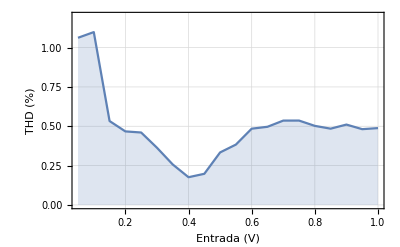

```mathematica
taD[ListLinePlot[#, PlotRange->{Full,{0, 1.2}}, PlotTheme->"Detailed", Filling->Axis,PlotRangePadding->0, FrameLabel->{"Entrada (V)", "THD (%)"}]&, {"A","THD"}]
```

```mathematica
taD[ListLinePlot[#, PlotRange->{Full,{0, 1.2}}, PlotTheme->"Detailed", Filling->Axis,PlotRangePadding->0, FrameLabel->{"Salida (V)", "THD (%)"}]&, {#["A"]28.25&,"THD"}]
```

```mathematica
SemanticImport["test.txt"][Length]
```

13418

```mathematica
Directory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri

```mathematica
ts2=SemanticImport[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]][All, Values]//Normal/*TimeSeries;
```

```mathematica
distortion[ts2]
```

0.0429719 %

```mathematica
Max[ts2]
```

1.40997

```mathematica
ts1=SemanticImport[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]][All, Values]//Normal/*TimeSeries;
```

```mathematica
Max[ts1]
```

39.7926

```mathematica
DeleteFile[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]];
```

```mathematica
distortion[ts1]
```

0.0815546 %

```mathematica
ts12u=SemanticImport[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]][All, Values]//Normal/*TimeSeries;
```

```mathematica
Max[ts12u]
```

39.7853

```mathematica
ListLinePlot[{ts1~TimeSeriesWindow~{1*^-3, 2*^-3},ts12u~TimeSeriesWindow~{1*^-3, 2*^-3}}//Apply[Subtract], PlotRange->Full]
```

```mathematica
distortion[ts12u]
```

0.858388 %

```mathematica
fpot=fftpot[ts12u];
```

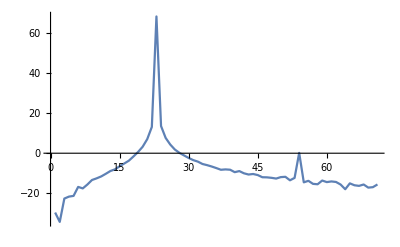

```mathematica
ListLinePlot[10 Log10@fpot[[10;;80]], PlotRange->Full]
```

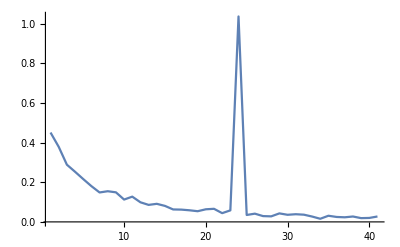

```mathematica
ListLinePlot[fpot[[40;;80]], PlotRange->Full]
```

```mathematica
potHarm[1,fftstep, 9][fpot]
```

6.9609×10^6

```mathematica
Table[potHarm[n,fftstep, 9][fpot], {n, 1, 5}]/.{fund_,harms___}:>√(Total[{harms}]/fund)
```

0.000747223

```mathematica
100/10^(100/20)//N
```

0.001

```mathematica
Table[potHarm[n,fftstep, 9][fpot], {n, 1, Min[50,Floor[ Length[fpot]/fftstep]]}]/.{fund_,harms___}:>√(Total[{harms}]/fund)
```

```mathematica
fftstep=First@Ordering[fftpot[ts12u], -1]-1
```

31

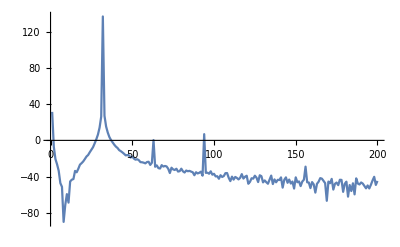

```mathematica
ListLinePlot[fftpot[ts12u]~Take~200//Log10//# 20&, PlotRange->Full]
```

```mathematica
ts2u2=SemanticImport[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]][All, Values]//Normal/*TimeSeries;
```

```mathematica
distortion[ts2u2]
```

0.0907039 %

```mathematica
distortion[ts2]
```

0.0429719 %

```mathematica
ListLinePlot[{ts2~TimeSeriesWindow~{1*^-3, 2*^-3},ts2u2~TimeSeriesWindow~{1*^-3, 2*^-3}}//Apply[Subtract], PlotRange->Full]
```

```mathematica
SemanticImport[FileNameJoin[{
NotebookDirectory[], "pruebas-rui", "pruebas.txt"
}]][All, Values]//Normal/*TimeSeries/*distortion
```

0.0269448 %

```mathematica
0.0039
```

aumentar el vaf mejora la distorsión un poco, pero no abajo del 0.3%. Supongo que es porque aumenta la ganancia de lazo. Sin embargo, no la arregla toda.

¿Cómo se mide la ganancia de lazo?

Ideas:
realimentar desde la segunda etapa nomás.

```mathematica
60/(40 5*^-3)
```

300

```mathematica
120/(40 5*^-3)
```

600

Sacar la realimentación sin cagar la polarización. Es decir, sacarla para continua. O sea, con un filtro pasabajos. Pero eso, ¿qué implica para la etapa de entrada? Borrarla, desaparecerla, ¿no?

Qué tocar para manejar el slew rate. Importante. Disipadores, embalamiento térmico.

Bajaron las corrientes de polarización porque tenían ruido.

```mathematica
5*^-3 1*^3
```

5

```mathematica
Abs[1/(ⅉ 2 π 5 c)]1000==10000//Solve/*N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-0.0031831},{c→0.0031831}}

```mathematica
Abs[1/(ⅉ 2 π 5 30.*^-6)]/10000
```

0.106103

Tiene que ser mayor a 366 para que en alterna siga siendo igual el feedback. Pero, menor a 10k o no sirve para nada

el realimentador, en total, tiene que atenuar 1 para continua, infinito para la alterna. Y tienen que verse 10k en continua para que se polarice sin offset. Suck it.

Cambiando la r del vas, aumenta la corriente de polarización y baja la distorsión hasta a lazo abierto, además de aumentar la gnaancia de lazo.
Simulando .tran 0 11m 1m 20n uic.
Para el caso normal, HDP, ahora da 0.029%. Para rvas=50, da 0.0044% (con corr de pol de 38mA aprox)
Para 10, 0.24%. Para 25, 0.01%
30, 0.007%, 40, 0.0048%, 50:0.044 60: 0.0046%
  65: 0.0049 68: 0.0042 70: 0.0039 71:0.0037 72:0.0038  73:0.0041 75:0.0047 80:0.006  90: 0.012
  71.5: 0.0046??? DALE!  70.5:00046

```mathematica
200/71 10.
```

28.169

```mathematica
3/x==2*^-3//Solve/*N
```

{{x→1500.}}

```mathematica
22/(610.7*^-9)
```

3.60242×10^7

```mathematica
0.3
```

```mathematica
1*^-3
```

1/1000

```mathematica
(1*^-3)/2 40 50000//N
```

1000.

```mathematica
1*^-3 10000
```

10

```mathematica
10*^-6 10*^3
```

1/10

```mathematica
par[x_, y_]:=(x y)/(x+y)
```

```mathematica
β(1/(40 5^-3)+550~par~(β (1/(40 26*^-3)+71.5)))/.β->60
```

29481.7

-14V, 54μA

```mathematica
50-14.08
```

35.92

```mathematica
35.92/rr==54.27*^-6//Solve//N
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rr→661876.}}

```mathematica
50-(33+ic 550+0.7)==vb
```

```mathematica
60.7 (550+15*^-3
```

El nuevo tiró distorsión casi 0.02%. Con corriente por VAS de 7mA. Y bastante clase B.
Ajustado para 10mA, da 0.016%
Haciendo más estable el mult de vbe, da también 0.016% así que fuck it
Aumentando para 14mA, cambió a 0.012%
Seguramente aumentando un cacho más se llega, así que lo hago y que la chupen. 
Subo la corriente a 23.5mA , 2.65V aprox el mult de vbe, y la dist da 0.01%

```mathematica
Quantity[1.7247*^7, "Volts"/"Seconds"]~UnitConvert~("Volts"/"Microseconds")
```

17.247 V/µs

```mathematica
Quantity[1.6*^7, "Volts"/"Seconds"]~UnitConvert~("Volts"/"Microseconds")
```

16. V/µs

```mathematica
Quantity[2 π 30000 40//N, "Volts"/"Seconds"]~UnitConvert~("Volts"/"Microseconds")
```

7.53982 V/µs

```mathematica
100. 10/7
```

142.857

```mathematica
20 Log10[28]//N
```

28.9432

```mathematica
(2.3-0.7)/rr==2*^-3//Solve
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rr→800.}}

```mathematica
1*^-3 rr==3//Solve
```

{{rr→3000.}}

```mathematica
Quantity[3.*^6, "Volts"/"Seconds"]~UnitConvert~("Volts"/"Microseconds")
```

3. V/µs

```mathematica
2 π 30000 40
```

7.53982×10^6

```mathematica
180-124
```

56

```mathematica
ts=SemanticImport["80k.txt"][All, Values]//Normal/*TimeSeries;
```

```mathematica
ListLinePlot[ts]
```

```mathematica
distortion[ts]
```

6.80926 %

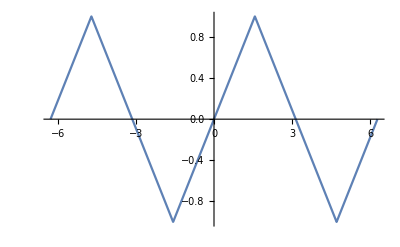

```mathematica
Plot[TriangleWave[t/(2 Pi)], {t, -2Pi, 2Pi}]
```

```mathematica
FourierCoefficient[TriangleWave[t/(2 Pi)], t, k]//Simplify
```

((-1)^k (-1+ⅈ^k)^3 (1+ⅈ^k))/(k^2 π^2)

```mathematica
fc[k_]:=((-1)^k (-1+ⅈ^k)^3 (1+ⅈ^k))/(k^2 π^2);
```

```mathematica
Abs[fc[1]]^2/Sum[Abs[fc[k]]^2, {k, 2, Infinity}]
```

96/(-96+π^4)

```mathematica
Sum[Abs[fc[k]]^2, {k, 2, Infinity}]/Abs[fc[1]]^2~UnitConvert~"Percent"//N
```

1.4678 %

```mathematica
Sinc[Pi/2 t]^2/.t->1
```

4/π^2

```mathematica
√(Sum[Sinc[Pi/2 t]^4, {t, 2, Infinity}]/(Sinc[Pi/2 t]^4/.t->1))//N
```

0.121153

```mathematica
96/(-96+π^4)//N
```

```mathematica
1/68.12902621863853
```

0.014678

```mathematica
con mvbe a 2.94
{{0.1, 0.0018
con mvbe a 2.72, da 0.0022
con mvbe a 2.56, da 0.0057
con mvbe a 2.56 y amplitud 1, da 0.024}}
```

```mathematica
dis={{0.001, 0.0001}, {0.01, 0.00026}, {0.1, 0.001}, {0.5, 0.01}, {1, 0.017}, {1.25, 0.027}, {1.41, 0.039}};
```

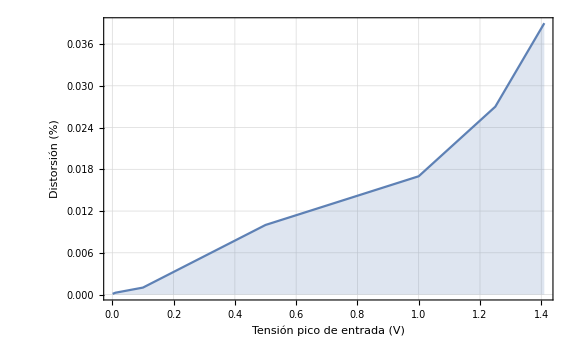

```mathematica
ListLinePlot[dis, PlotTheme->"Detailed", FrameLabel->{"Tensión pico de entrada (V)", "Distorsión (%)"}, ImageSize->Large, Filling->Axis, PlotRangePadding->{{0,0}, {0,0}}]
```

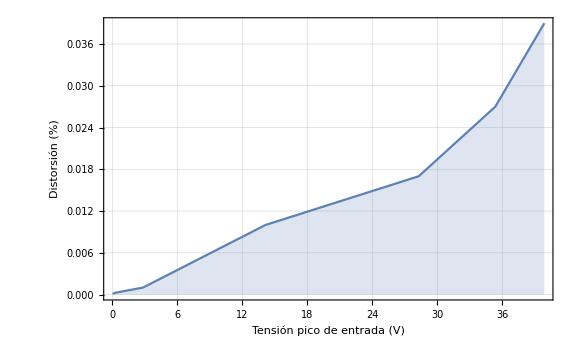

```mathematica
ListLinePlot[dis/.{x_, y_}:>{x 40/(√2), y}, PlotTheme->"Detailed", FrameLabel->{"Tensión pico de salida (V)", "Distorsión (%)"}, ImageSize->Large, Filling->Axis, PlotRangePadding->{{0,0.1}, {0,0.001}}]
```

```mathematica
Directory[]
```

/home/rui

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri

```mathematica
ts=SemanticImport["../rui/ampli.txt"][All, Values]//Normal/*TimeSeries;
```

```mathematica
distortion[ts]
```

0.115951 %

```mathematica
vs=ts@N@Range[0, ts["LastTime"], 1*^-6];
```

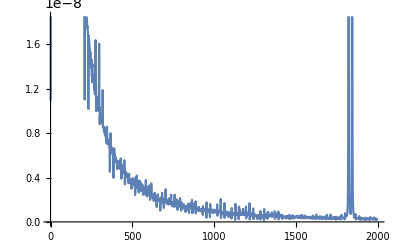

```mathematica
ListLinePlot[Take[Abs[Fourier[vs]]^2,{2, 2000}]]
```

```mathematica
SetAttributes[sumPotdB, Flat];
```

```mathematica
ClearAll[sumPotdB];
```

```mathematica
sumPotdB[x_, y_]:=10 Log10[10^(x/10)+10^(y/10)];
sumPotdB[x_, y_, z__]:=sumPotdB[x, sumPotdB[y, z]];
```

```mathematica
fourier[ts_TemporalData]:=With[{tsreg=TimeSeriesResample[ts]},
TimeSeries[Fourier[tsreg["Values"],FourierParameters->{1, -1}], {0, 1/MinimumTimeIncrement[tsreg]}]/.f_:>
TimeSeriesWindow[f, {0, f["LastTime"]/2}]
];
```

```mathematica
fts=fourier[ts];
```

```mathematica
fts=fts~TimeSeriesWindow~{0, 50000};
```

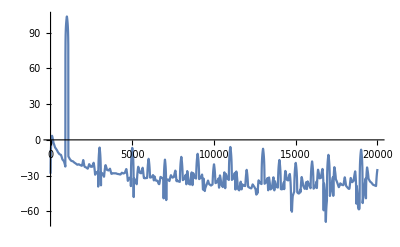

```mathematica
Plot[10 Log10[Abs[fts[frec]]^2], {frec, 0, 20*^3}, PlotRange->Full]
```

```mathematica
bla[k_]:=NIntegrate[Abs[fts[f]]^2, {f, k 1000-50, k 1000+50}]
```

```mathematica
bla[1]
```

1.33398×10^12

```mathematica
√(Total[bla/@Range[2, 20]]/bla[1])100.
```

0.000746634

```mathematica
NIntegrate[Abs[fts[f]]^2, {f, 950, 1050}]
```

```mathematica
fts[2000]
```

-0.120519+0.0778772 ⅈ